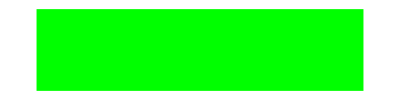

```mathematica
Graphics[
Style[Rectangle[{0,0},{20,5}],Green]
]
```

```mathematica
achtergrond=Graphics[{EdgeForm[Directive[Thick,Gray]],Transparent,Rectangle[{0,0},{20,5}]}]
```

-Graphics-

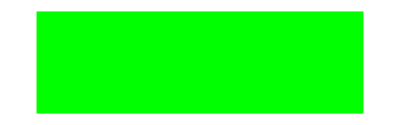

```mathematica
links=Graphics[{Green,Rectangle[{0,0},{16,5}]}]
```

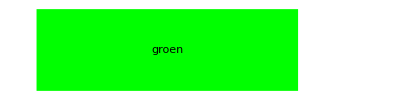

```mathematica
Show[{links,labeltje,achtergrond}]
```

```mathematica
labeltje=Graphics[Text["groen",{8,2.5}]];
```

```mathematica
Verdeling[waardes_]:=Module[{},
col={Red,Blue,Orange,Green,Brown,Purple};
w=500;
h=100;
achtergrond=Graphics[{EdgeForm[Directive[Thick,Gray]],Transparent,Rectangle[{0,0},{w,h}]}];
tot=Total[waardes];
Motor=Graphics[{col[[1]],Rectangle[{0,0},{w*(waardes[[1]]/tot),h}]}];
Rem=Graphics[{col[[2]],Rectangle[{w*(waardes[[1]]/tot),0},{w*(waardes[[2]]/tot),h}]}];
Rol=Graphics[{col[[3]],Rectangle[{w*(waardes[[2]]/tot),0},{w*(waardes[[3]]/tot),h}]}];
Lucht=Graphics[{col[[4]],Rectangle[{w*(waardes[[3]]/tot),0},{w*(waardes[[4]]/tot),h}]}];
Show[Motor,Rem,Rol,Lucht,achtergrond]

];
Verdeling[{8,12,30,20}]
```

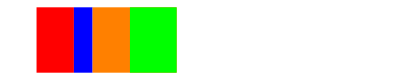

```mathematica
RGBColor
```

```mathematica
kilowattuur=100;
liter=80;
```

```mathematica
verliezen={5,12,43,33};
```

```mathematica
fracties[lijst_]:=({#*kilowattuur,#*liter})&/@(lijst/Total[lijst])
```

```mathematica
fractie[verliezen]
```

{5/93,4/31,43/93,11/31}

```mathematica
({#*kilowattuur,#*liter})&/@fractie[verliezen]
```

{{500/93,400/93},{400/31,320/31},{4300/93,3440/93},{1100/31,880/31}}

```mathematica
fracties[verliezen]
```

{{500/93,400/93},{400/31,320/31},{4300/93,3440/93},{1100/31,880/31}}

```mathematica
label[kWh_,L_]:=Style[Text[Grid[{{Round[kWh,1],"kWh/100km"},{Round[L,1],"L/100km"}},Alignment->"/"]],
 FontSize->15,FontFamily->"Georgia"]
```

```mathematica
label[21.12342,30]
```

21 | kWh/100km
30 | L/100km

```mathematica
Clear[verliezen]
```

```mathematica
labelmaker[verliezen_]:=Table[Tooltip[verliezen[[i]],label[fracties[verliezen][[i,1]],fracties[verliezen][[i,2]]]],{i,1,Length[verliezen]}]
```

```mathematica
labelmaker[verliezen]
```

{5,12,43,33}

```mathematica
Length[verliezen]
```

4

```mathematica
verliezen[[1]]
```

5

```mathematica
Tooltip[verliezen[[1]],label[fracties[verliezen][[1,1]],fracties[verliezen][[1,2]]]]
```

5

```mathematica
Clear[label]
```

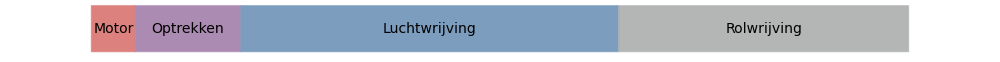

```mathematica
BarChart[{labelmaker[verliezen]},ChartLayout->"Stacked",BarOrigin->Left,Axes->False,AspectRatio->1/16,ImageSize->IS,ChartStyle->{Lighter[CTOT],Lighter[Crem],Lighter[Clucht],Lighter[Crol]},
ChartLabels->{"Motor","Optrekken","Luchtwrijving","Rolwrijving"},LabelStyle->LS]
```

```mathematica
BarChart[{{3.65-3.47,0.47,0.95,Tooltip[2.04,label]}},ChartLayout->"Stacked",BarOrigin->Left,Axes->False,AspectRatio->1/16,ImageSize->IS,ChartStyle->{Lighter[CTOT],Lighter[Crem],Lighter[Clucht],Lighter[Crol]},
ChartLabels->{"Motor","Optrekken","Luchtwrijving","Rolwrijving"},LabelStyle->LS]
```

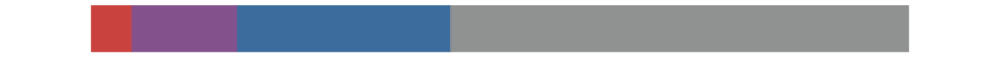

```mathematica
BarChart[{{3.65-3.47,0.47,0.95,2.04}},ChartLayout->"Stacked",BarOrigin->Left,Axes->False,AspectRatio->1/16,ImageSize->IS,ChartStyle->{CTOT,Crem,Clucht,Crol}]
```

```mathematica
Manipulate[BarChart[{{a,b,c,d},{a,b}},ChartLayout->"Stacked",BarOrigin->Left,Axes->False,AspectRatio->1/8,ImageSize->400,ChartStyle->{Green,Black,Orange,Blue},ChartLabels->{"eerste","tweede","derde","vierde"},Joined->True],{a,1,10},{b,1,10},{c,1,10},{d,1,10}]
```

32 gallon to litre

WolframAlphaQueryResults

18.5 gallon to litre

WolframAlphaQueryResults

245 miles to km

WolframAlphaQueryResults